```mathematica
a=Import["~/SL_2024-03-13_H11_M34_S52/L_2024-03-13_H11_M34_S52nz.csv","CSV"];
```

```mathematica
Dimensions[a]
```

{91498,11}

```mathematica
at=Transpose[a];
```

```mathematica
Dimensions[at]
```

{11,91498}

## N = 10000~40000

## cross correlation (2) / Tc 4 vs Tc 5

```mathematica
b1=Table[at[[4,i]],{i,10000,40000}];
```

```mathematica
b2=Table[at[[5,i]],{i,10000,40000}];
```

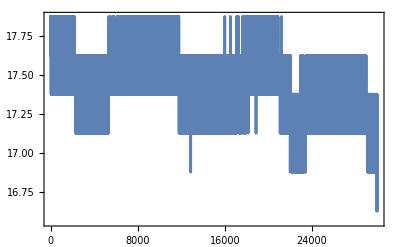

```mathematica
ListPlot[b1,Joined->True,PlotRange->All,Axes->False,Frame->True]
```

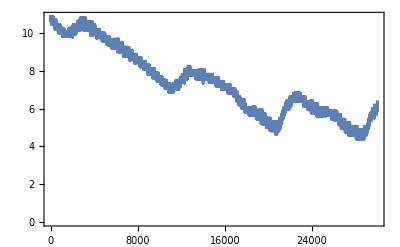

```mathematica
ListPlot[b2,Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
f1=Fourier[b1];
```

```mathematica
f2=Conjugate[Fourier[b2]];
```

```mathematica
ff=f1*f2;
```

```mathematica
c1=Re[InverseFourier[ff]]/(Norm[b1]Norm[b2]);
```

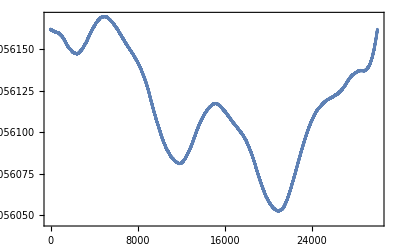

```mathematica
ListPlot[Re[c1],Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
mc=Max[c1]
```

0.00561697

```mathematica
z=0;
```

```mathematica
Do[If[c1[[i]]==mc,z=i],{i,Length[c1]}]
```

```mathematica
Print[z]
```

4997

## cross correlation (2) / Tc 6 vs Tc 7

```mathematica
b1=Table[at[[6,i]],{i,10000,40000}];
```

```mathematica
b2=Table[at[[7,i]],{i,10000,40000}];
```

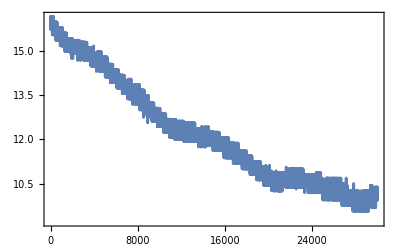

```mathematica
ListPlot[b1,Joined->True,PlotRange->All,Axes->False,Frame->True]
```

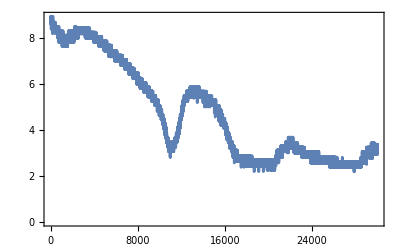

```mathematica
ListPlot[b2,Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
f1=Fourier[b1];
```

```mathematica
f2=Conjugate[Fourier[b2]];
```

```mathematica
ff=f1*f2;
```

```mathematica
c1=Re[InverseFourier[ff]]/(Norm[b1]Norm[b2]);
```

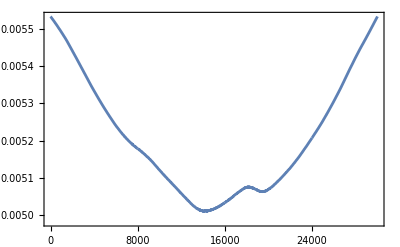

```mathematica
ListPlot[Re[c1],Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
mc=Max[c1]
```

0.0055346

```mathematica
z=0;
```

```mathematica
Do[If[c1[[i]]==mc,z=i],{i,Length[c1]}]
```

```mathematica
Print[z]
```

1